# network exp. MOT beam alignment

P. Huft

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 2023.01.03

The femtowatt detector was used to get 1D scans of the MOT and excitation beams along different directions. These scans were done manually by incrementing the NanoMax micrometer knobs by 50 μm or 100 μm at a time for the excitation or MOT beams, respectively. The positions recorded below are wrt the location of the parabolic mirror focal spot. The uncertainty in this should be no more than 2 μm, but most of the time it was under 1 μm. The directions scanned were Y, which is along the parabolic mirror tube axis, and Z, which is perpendicular to the plane of the bridge. I did the 2 1D scans for MOT 1, MOT 4, and both GRIN beams. MOT 1 and 4 still coupled at least a few percent each into the opposite MOT tube so I didn’t scan those.

```mathematica
MOT1Zμm=Range[-500,500,100];
MOT1ZmV={13,34,52,83,95.6,156,185,180,130,90,60};
MOT1Yμm=Range[-500,400,100];
MOT1YmV={40,70,125,145,196,160,120,94,45,25};
MOT4Zμm=Range[-500,600,100];
MOT4ZmV={7,14,20,45,73,100,145,150,125,90,72,19};
MOT4Yμm=Range[-500,400,100];
MOT4YmV=Join[{22,25,47,76,90,135},{105,76,58,50}*135/112];
G1Zμm=Range[-300,400,50];
G1ZmV={5,12,20,34,44,66,85,105,108,113,87,80,50,63,47};
G1Yμm=Range[-250,250,50];
G1YmV={8,15,25,45,70,91,81,57,40,16,12};
G2Zμm=Range[-300,450,50];
G2ZmV={22,47,95,165,280,480,760,955,1050,970,880,616,370,320,180,60};
G2Yμm=Range[-300,300,50];
G2YmV={25,54,135,265,450,605,750,630,540,303,144,65,50};

MOT1Zdata=Transpose@{MOT1Zμm,MOT1ZmV};
MOT1Ydata=Transpose@{MOT1Yμm,MOT1YmV};
MOT4Zdata=Transpose@{MOT4Zμm,MOT4ZmV};
MOT4Ydata=Transpose@{MOT4Yμm,MOT4YmV};
G1Zdata=Transpose@{G1Zμm,G1ZmV};
G1Ydata=Transpose@{G1Yμm,G1YmV};
G2Zdata=Transpose@{G2Zμm,G2ZmV};
G2Ydata=Transpose@{G2Yμm,G2YmV};
```

```mathematica
Zdata={MOT1Zdata,MOT4Zdata,G1Zdata,G2Zdata};
Ydata={MOT1Ydata,MOT4Ydata,G1Ydata,G2Ydata};
model=a Exp[(-(x-x0)^2)/w^2];
Zfits={};
Yfits={};
legend={"MOT1","MOT4","GRIN1","GRIN2"};
For[i=1,i<Length[Zdata]+1,i++,
Zfit=FindFit[Zdata[[i]],model,{{a,Max[(Transpose@Zdata[[i]])[[2]]]},{w,100},{x0,0}},x];
Yfit=FindFit[Ydata[[i]],model,{{a,Max[(Transpose@Ydata[[i]])[[2]]]},{w,100},{x0,0}},x];
Print[legend[[i]],":"];
Print["Z fit:",Zfit];
Print["Y fit:",Yfit];
AppendTo[Zfits,Zfit];
AppendTo[Yfits,Yfit];
]
```

MOT1:

Z fit:{a→176.579,w→356.946,x0→122.664}

Y fit:{a→177.846,w→334.589,x0→-86.9605}

MOT4:

Z fit:{a→146.46,w→336.289,x0→178.78}

Y fit:{a→122.308,w→365.105,x0→51.3149}

GRIN1:

Z fit:{a→106.306,w→258.206,x0→124.969}

Y fit:{a→86.1421,w→149.46,x0→13.5817}

GRIN2:

Z fit:{a→1036.29,w→196.604,x0→114.949}

Y fit:{a→716.076,w→157.579,x0→7.24966}

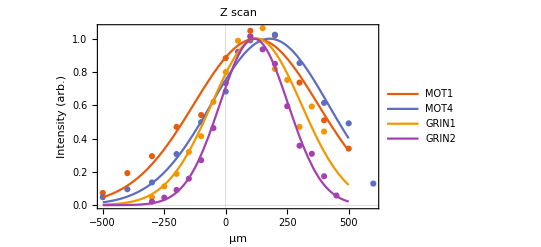

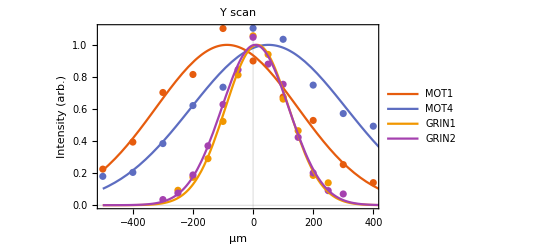

```mathematica
pltZ=Show[ListPlot[Array[Transpose@{(Transpose@Zdata[[#]])[[1]],(Transpose@Zdata[[#]])[[2]]/Values[Zfits[[#,1]]]}&,Length[Zfits]],PlotLabel->"Z scan",PlotTheme->"Scientific",FrameLabel->{"μm","Intensity (arb.)"},FrameStyle->Directive[Black,Medium]],Plot[Evaluate[Array[(model/.Zfits[[#]])/Values[Zfits[[#,1]]]&,Length[Zfits]]],{x,-500,500},PlotRange->All,PlotLegends->legend,PlotTheme->"Scientific"]]
pltY=Show[ListPlot[Array[Transpose@{(Transpose@Ydata[[#]])[[1]],(Transpose@Ydata[[#]])[[2]]/Values[Yfits[[#,1]]]}&,Length[Yfits]],PlotLabel->"Y scan",PlotTheme->"Scientific",FrameLabel->{"μm","Intensity (arb.)"},FrameStyle->Directive[Black,Medium]],Plot[Evaluate[Array[(model/.Yfits[[#]])/Values[Yfits[[#,1]]]&,Length[Yfits]]],{x,-500,500},PlotRange->All,PlotLegends->legend,PlotTheme->"Scientific"]]
```

```mathematica
Export["M1_M4_G1_G2_fiberscanZ.svg",pltZ]
Export["M1_M4_G1_G2_fiberscanY.svg",pltY]
```

M1_M4_G1_G2_fiberscanZ.svg

M1_M4_G1_G2_fiberscanY.svg

## 2022.12.14

### MOT beams 1, 2, and 4

The camera is looking along the optical axis of MOT beam 1 (from the side of MOT beam 3)

```mathematica
data=ImageData[Import["MOT 1 1156_20221214.bmp"]];
Image[data]
```

-Graphics-

```mathematica
Colorize[Image[data],ColorFunction->(Blend[{Black,Red},#]&)]
```

-Graphics-

```mathematica
files={
"MOT 1 1156_20221214.bmp",
"MOT 2 1155_20221214.bmp",
"MOT 4 1200_20221214.bmp"};
images={};
colorimages={};
RGBcolors={{1,0,0},{1,0,1},{0,0.5,1}};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[377;;377+350,360;;360+350,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
colordata=TensorProduct[normdata,RGBcolors[[i]]];
Print[Image[colordata,ColorSpace->"RGB"]];
AppendTo[colorimages,colordata];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[normdata];
(*images={};
colors={Red,Green,Blue};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[377;;377+350,360;;360+350,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Colorize[Image[normdata],ColorFunction->(Blend[{Black,colors[[i]]},#]&)]];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[images[[1]]];*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
(*rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]*)
Image[Total[colorimages],ColorSpace->"RGB"]
```

-Graphics-

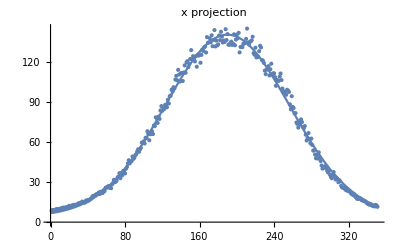

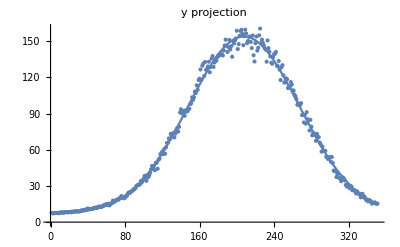

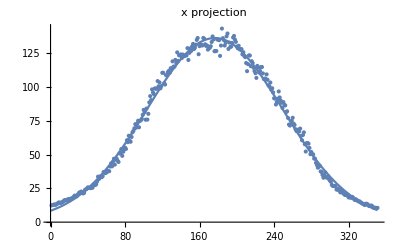

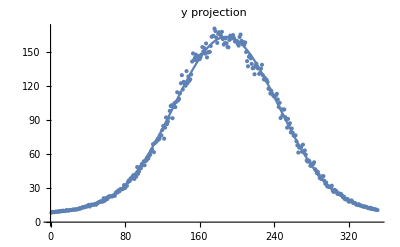

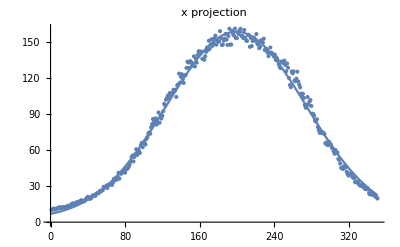

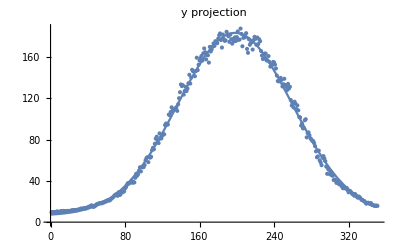

```mathematica
xprojections={};
yprojections={};
xfits={};
yfits={};
model=a Exp[-(x-x0)^2/b]+c;
For[i=1,i<Length[images]+1,i++,
xproj=Total[images[[i]],{1}];
yproj=Total[images[[i]],{2}];
AppendTo[xprojections,xproj];
AppendTo[yprojections,yproj];
xfit=FindFit[xproj,model,{{a,Max[xproj]},{b},{c,Min[xproj]},{x0,200}},x];
yfit=FindFit[yproj,model,{{a,Max[yproj]},{b},{c,Min[yproj]},{x0,200}},x];
Print[Show[ListPlot[xproj,PlotLabel->"x projection"],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]];
Print[Show[ListPlot[yproj,PlotLabel->"y projection"],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]];
]
```

{MOT 1,MOT 2,MOT 4}

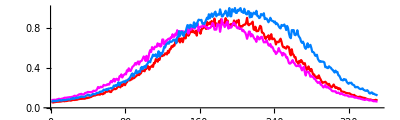

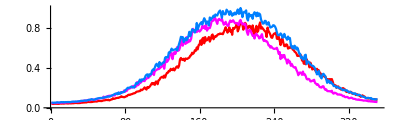

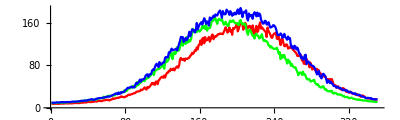

```mathematica
leg={"MOT 1","MOT 2", "MOT 4"}
ListPlot[xprojections/Max[xprojections],PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 15]]
ListPlot[yprojections/Max[yprojections],PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 15]]
```

## 2022.12.13

### MOT 1, GRIN 2, and GRIN 1P

The camera is looking along the optical axis of MOT beam 1 (from the side of MOT beam 3). GRIN 2 (GRIN 1P) is on the left (right) side of the bridge (if the mirror is on the bottom when looking down at the bridge).

```mathematica
data=ImageData[Import["MOT 1 1608_20221213.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
"MOT 1 1608_20221213.bmp",
"GRIN 2 1605_20221213.bmp",
"GRIN 1P 1604_20221213.bmp"};
(*images={};
colors={Red,Green,Blue};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[503;;503+350,523;;523+350,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Colorize[Image[normdata],ColorFunction->(Blend[{Black,colors[[i]]},#]&)]];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[images[[1]]];*)
```

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
(*rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]*)
```

```mathematica
images={};
colorimages={};
RGBcolors={{1,0,0},{1,0,1},{0,0.5,1}};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[503;;503+350,523;;523+350,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
colordata=TensorProduct[normdata,RGBcolors[[i]]];
Print[Image[colordata,ColorSpace->"RGB"]];
AppendTo[colorimages,colordata];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[normdata];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Image[Total[colorimages],ColorSpace->"RGB"]
```

-Graphics-

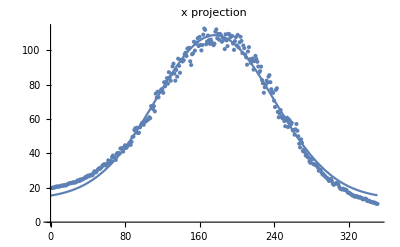

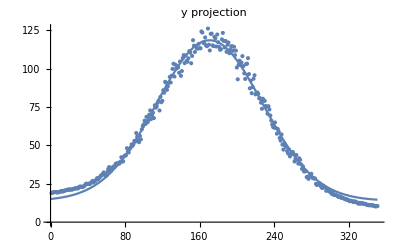

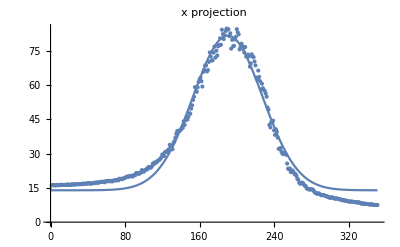

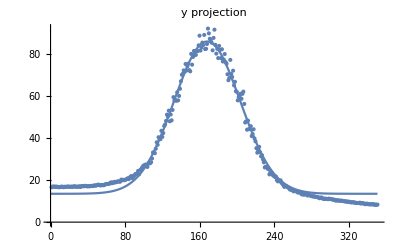

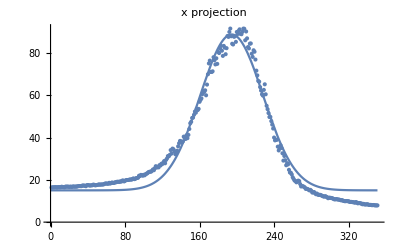

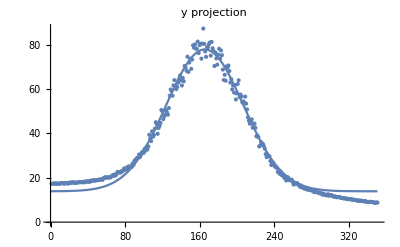

```mathematica
xprojections={};
yprojections={};
xfits={};
yfits={};
model=a Exp[-(x-x0)^2/b]+c;
For[i=1,i<Length[images]+1,i++,
xproj=Total[images[[i]],{1}];
yproj=Total[images[[i]],{2}];
AppendTo[xprojections,xproj];
AppendTo[yprojections,yproj];
xfit=FindFit[xproj,model,{{a,Max[xproj]},{b},{c,Min[xproj]},{x0,200}},x];
yfit=FindFit[yproj,model,{{a,Max[yproj]},{b},{c,Min[yproj]},{x0,200}},x];
Print[Show[ListPlot[xproj,PlotLabel->"x projection"],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]];
Print[Show[ListPlot[yproj,PlotLabel->"y projection"],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]];
]
```

{MOT 1,GRIN 2,GRIN 1P}

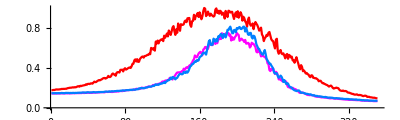

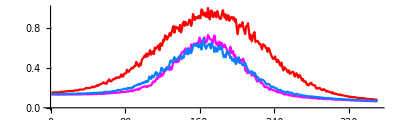

```mathematica
leg={"MOT 1","GRIN 2", "GRIN 1P"}
ListPlot[xprojections/Max[xprojections],PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 15]]
ListPlot[yprojections/Max[yprojections],PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 15]]
```

## 2022.12.09

### MOT beam 1, GRIN 2, and mirror focus on transparency sheet 4

GRIN 2 replaced GRIN 1 after we had made a mistake aligning the polarization and had to break GRIN 1 off of the bridge.

```mathematica
data=ImageData[Import["MOT 1 1652_20221209.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 1652_20221209.bmp",
"GRIN 2 1651_20221209.bmp",
"mirror focus 1649_20221209.bmp"};
images={};
colorimages={};
RGBcolors={{1,0,0},{1,0,1},{0,0.5,1}};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[640;;640+130,640;;640+130,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
colordata=TensorProduct[normdata,RGBcolors[[i]]];
Print[Image[colordata,ColorSpace->"RGB"]];
AppendTo[colorimages,colordata];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[normdata];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Image[Total[colorimages],ColorSpace->"RGB"]
```

-Graphics-

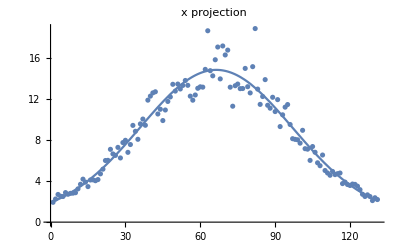

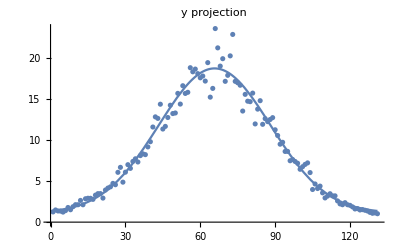

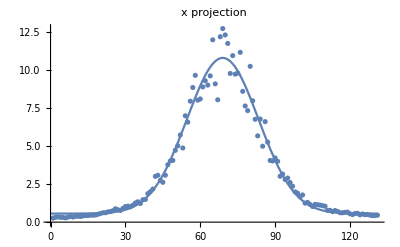

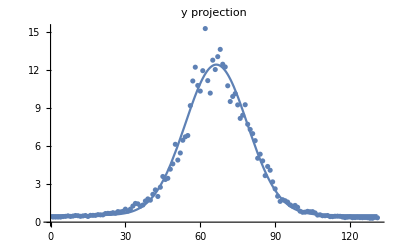

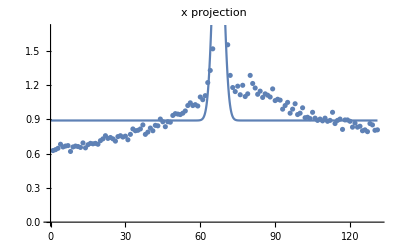

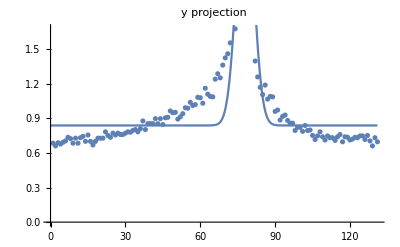

```mathematica
xprojections={};
yprojections={};
xfits={};
yfits={};
model=a Exp[-(x-x0)^2/b]+c;
scaling={1,1,4};
background={0,0,2.5};
For[i=1,i<Length[images]+1,i++,
xproj=Total[images[[i]],{1}];
yproj=Total[images[[i]],{2}];
AppendTo[xprojections,xproj*scaling[[i]]-background[[i]]];
AppendTo[yprojections,yproj*scaling[[i]]-background[[i]]];
xfit=FindFit[xproj,model,{{a,Max[xproj]},{b},{c,Min[xproj]},{x0,70}},x];
yfit=FindFit[yproj,model,{{a,Max[yproj]},{b},{c,Min[yproj]},{x0,70}},x];
Print[Show[ListPlot[xproj,PlotLabel->"x projection"],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]];
Print[Show[ListPlot[yproj,PlotLabel->"y projection"],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]];
]
```

```mathematica
Map[RGBColor,RGBcolors]
```

{RGBColor[{1, 0, 0}],RGBColor[{1, 0, 1}],RGBColor[{0, 0.5, 1}]}

{MOT 1,GRIN 2,Mirror}

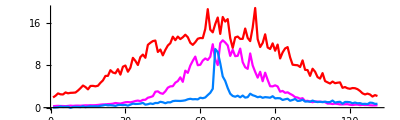

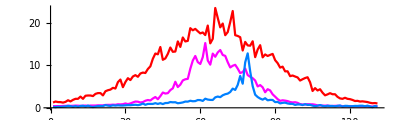

```mathematica
leg={"MOT 1", "GRIN 2","Mirror"}
ListPlot[xprojections,PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 14]]
ListPlot[yprojections,PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->Map[RGBColor,RGBcolors],AspectRatio->0.3,AxesStyle->Directive[Black, 14]]
```

```mathematica
`
```

## 2022.12.06

### MOT beam 1, GRIN 1, and mirror focus on transparency sheet 4

Transparency sheet 4 was rinsed with acetone and blown off with canned air. The GRIN lens has been glued at this point (MOT 1 was glued a while ago).

```mathematica
data=ImageData[Import["MOT 1 1146_20221206.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
"mirror focus 1144_20221206.bmp",
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 1146_20221206.bmp",
"GRIN 1 1145_20221206.bmp"};
images={};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[700;;700+250,480;;480+250,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[images[[1]]];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]
```

-Graphics-

## 2022.11.23

### MOT beam 1, GRIN 1, and mirror focus on transparency sheet 3

Transparency sheet 3 was rinsed with acetone and blown off with canned air. The GRIN assembly has not been rotated to give the correct polarization angle, but has been aligned to the mirror focus and MOT beam 1 by rotating it by hand while it was loosely clamped to the bridge. It is possible that the optimal position and optimal polarization angle are mutually incompatible, but I have not tested this yet.

```mathematica
data=ImageData[Import["MOT 1 952_20221123.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
"parabolic mirror focus 953_20221123.bmp",
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 952_20221123.bmp",
"grin1 951_20221123.bmp"};
images={};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[560;;720,370;;530,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[images[[1]]];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]
```

-Graphics-

## 2022.11.21

### MOT beam 1, 4, and mirror focus on transparency sheet 2

Transparency sheet rinsed (not wiped) with acetone and inserted into the mirror tube. ThorCam looking down the right side excitation axis with TV Zoom lens (the f=8-50ish mm one).  In hind-sight, it is clear that the speckle pattern is because my aperture was too small, giving a large depth of field, so I was actually imaging the far field.

```mathematica
data=ImageData[Import["MOT 4 1800_20221121.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
"parabolic mirror focus 1756_20221121.bmp",
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 1755_20221121.bmp",
"MOT 4 1800_20221121.bmp"};
images={};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[590;;770,480;;660,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
AppendTo[images,normdata];
]
{xdim,ydim}=Dimensions[images[[1]]];
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]
```

-Graphics-

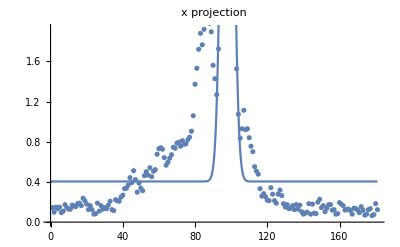

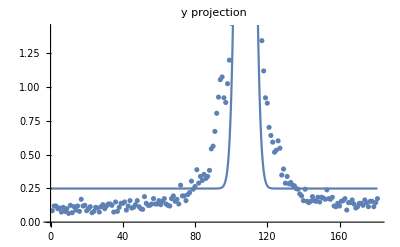

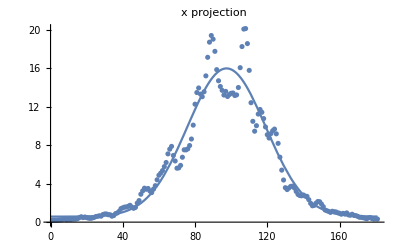

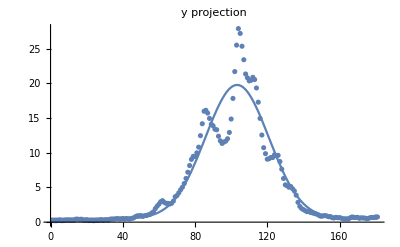

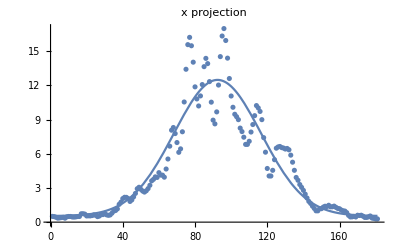

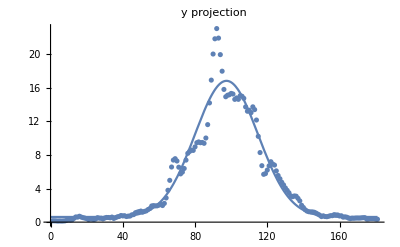

```mathematica
xprojections={};
yprojections={};
xfits={};
yfits={};
model=a Exp[-(x-x0)^2/b]+c;
For[i=1,i<Length[images]+1,i++,
xproj=Total[images[[i]],{1}];
yproj=Total[images[[i]],{2}];
AppendTo[xprojections,xproj];
AppendTo[yprojections,yproj];
xfit=FindFit[xproj,model,{{a,Max[xproj]},{b},{c,Min[xproj]},{x0,100}},x];
yfit=FindFit[yproj,model,{{a,Max[yproj]},{b},{c,Min[yproj]},{x0,100}},x];
Print[Show[ListPlot[xproj,PlotLabel->"x projection"],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]];
Print[Show[ListPlot[yproj,PlotLabel->"y projection"],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]];
]
```

```mathematica
aGuess
```

16.9843

{mirror tube beam,MOT 1,MOT 4}

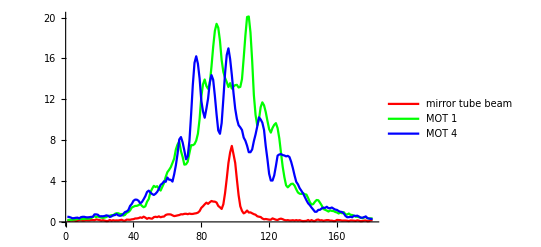

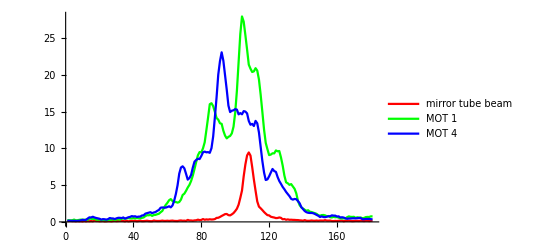

```mathematica
leg={"mirror tube beam","MOT 1", "MOT 4"}
ListPlot[xprojections,PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->{Red,Green,Blue}]
ListPlot[yprojections,PlotLegends->leg,Joined->True,PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

### MOT beam 1, 4, and mirror focus on transparency sheet 1

Transparency sheet wiped with acetone and inserted into the mirror tube. ThorCam looking down the right side excitation axis with TV Zoom lens (the f=8-50ish mm one). This demonstrates the method as proof of principle.

```mathematica
data=ImageData[Import["MOT 4 940_20221121.bmp"]];
Image[data]
```

-Graphics-

```mathematica
files={
"parabolic mirror focus 937_20221121.bmp",
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 943_20221121.bmp",
"MOT 4 940_20221121.bmp"};
images={};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[610;;780,380;;530,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
AppendTo[images,normdata];
]
```

-Graphics-

-Graphics-

-Graphics-

## 2022.11.17

### MOT beams 1, 4, and mirror hole beam on tape

```mathematica
data=ImageData[Import["MOT 1 20221117.bmp"]];
Image[data]
```

-Graphics-

```mathematica
Image[data[[400;;750,600;;950,1]]]
```

-Graphics-

```mathematica
files={
"mirror tube 20221117.bmp",
(*"MOT 1 4 and mirror tube 20221117.bmp",*)
"MOT 1 20221117.bmp",
"MOT 4 20221117.bmp"};
images={};
For[i=1,i<Length[files]+1,i++,
data=ImageData[Import[files[[i]]]][[400;;750,600;;950,1]];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
AppendTo[images,normdata];
]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[xs,ys,μx,μy,t];
model=Exp[-((x Cos[t]-y Sin[t]-μx)/xs)^2-((y Cos[t]+x Sin[t]- μy)/ys)^2]
(*FindFit[images[[1]],model,{}]*)
```

ⅇ^(-(-μy+y Cos[t]+x Sin[t])^2/ys^2-(-μx+x Cos[t]-y Sin[t])^2/xs^2)

```mathematica
f=ImageData[ImageRotate[Image[images[[1]]],-π/2]];
{xdim,ydim}=Dimensions[f];
fitdata=Flatten[Table[{i,j,f[[i,j]]},{i,Range[xdim]},{j,Range[ydim]}],1];
f=images[[1]];
```

```mathematica
fit=FindFit[fitdata,model,{{xs,25},{ys,50},{t,-0.15},{μx,175},{μy,140}},{x,y}]
Show[(*ImageRotate[*)Image[f](*,π/2]*),ContourPlot[model/.fit,{x,1,xdim},{y,1,ydim},PlotRange->All,ContourShading->None,ContourStyle->Red]]
{xmax,ymax}=Values[NSolve[{((x Cos[t]-y Sin[t]-μx)/xs)^2==0,((y Cos[t]+x Sin[t]- μy)/ys)^2==0}/.fit,{x,y}][[1]]];
rmax=ydim-Floor[ymax+0.5];
cmax=Floor[xmax+0.5];
```

{xs→16.8809,ys→31.7478,t→-0.271749,μx→189.165,μy→112.775}

-Graphics-

```mathematica
Show[Image[f],ListPlot[{{xmax,ymax}},PlotStyle->Red]]
```

-Graphics-

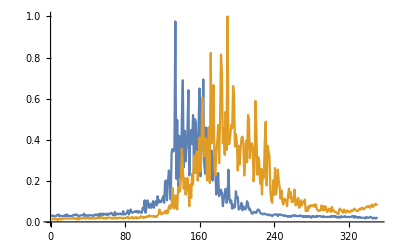

```mathematica
ListPlot[{f[[rmax,;;]],f[[;;,cmax]]},PlotRange->All,Joined->True]
```

```mathematica
Clear[i]
```

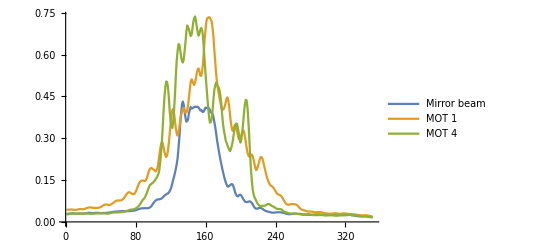

```mathematica
(*slice perp. to mirror beam axis*)
ListPlot[Table[GaussianFilter[images[[i]][[rmax,;;]],5],{i,Range[Length[images]]}],PlotRange->All,Joined->True,PlotLegends->{"Mirror beam","MOT 1","MOT 4"}]
```

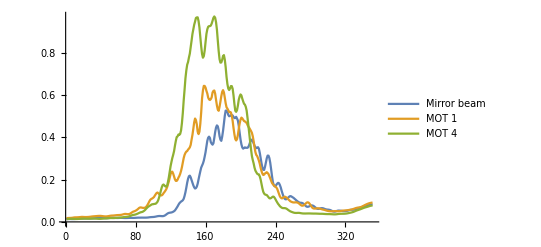

```mathematica
(*slice along to mirror beam axis. *)
ListPlot[Table[GaussianFilter[images[[i]][[;;,cmax]],5],{i,Range[Length[images]]}],PlotRange->All,Joined->True,PlotLegends->{"Mirror beam","MOT 1","MOT 4"}]
```

```mathematica
Show[images[[1]],images[[2]],images[[3]]]
```

Show::gcomb: Could not combine the graphics objects in Show[{{0.0403226,0.0443548,0.0443548,0.0483871,0.0403226,0.0483871,0.0443548,0.0443548,0.0403226,0.0403226,«341»},{0.0443548,0.0443548,0.0403226,0.0403226,0.0443548,0.0403226,0.0443548,0.0483871,0.0403226,0.0483871,«341»},«7»,{0.0443548,0.0403226,0.0403226,0.0443548,0.0403226,0.0403226,0.0403226,0.0403226,0.0403226,0.0483871,«341»},«341»},{«1»},{{0.0443548,0.0443548,«7»,0.0483871,«341»},{«1»},«8»,«341»}].

Show[1]
 |  |  |  |

```mathematica
(*rgb = mirror tube beam, MOT beam 1, MOT beam 4. mirror tube beam scaled for brightness*)
rgbData=Table[{2*images[[1]][[r,c]],images[[2]][[r,c]],images[[3]][[r,c]]},{r,Range[ydim]},{c,Range[xdim]}];
Image[rgbData]
```

-Graphics-

Akbar suggested getting the center of each image not with a 2D Gaussian fit as I was doing by projecting each image on the x and y axes.

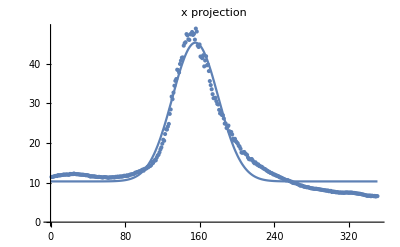

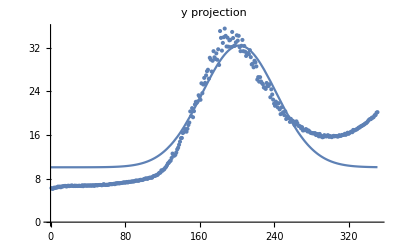

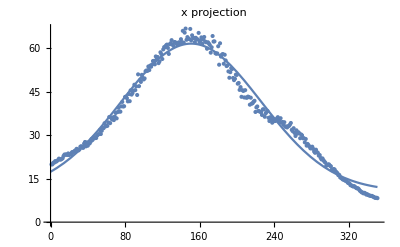

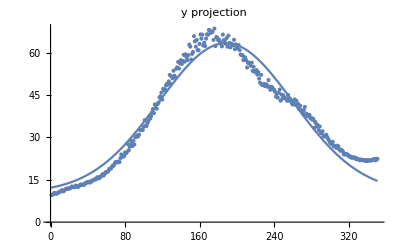

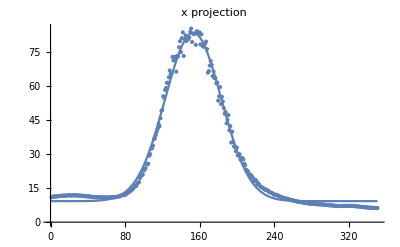

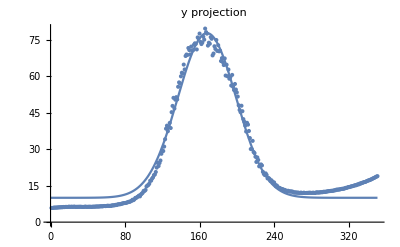

{{11.4113,11.4073,11.4879,11.5444,11.6492,11.6815,11.6331,11.8669,11.7944,11.8145,11.8266,11.9073,11.9032,12.0444,11.9677,11.9839,12.0403,12.0242,11.9798,11.9556,12.1774,12.1048,12.1613,12.1169,12.2823,12.1774,12.1371,12.0766,12.1169,12.0605,12.0403,12.004,11.9758,11.9677,11.9798,11.9234,11.9032,11.8226,11.879,11.7984,11.7621,11.6129,11.4798,11.6169,11.5444,11.5202,11.5847,11.4395,11.4718,11.3992,11.375,11.4435,11.3952,11.3589,11.3145,11.2581,11.3347,11.379,11.3548,11.2984,11.2863,11.1734,11.2823,11.2984,11.2702,11.3145,11.3508,11.2944,11.2863,11.4435,11.371,11.5081,11.4032,11.5,11.5403,11.4798,11.5444,11.5645,11.7137,11.6815,11.6331,11.8306,11.6774,11.7984,11.9597,12.0161,12.0484,12.1048,12.1331,12.2702,12.4919,12.4758,12.6532,12.625,12.8427,12.746,12.9879,13.0927,13.2782,12.996,13.4597,13.4919,13.5766,13.9395,13.8508,14.2823,14.1694,14.3831,15.1492,14.9113,15.3427,15.7056,15.6048,16.2944,16.8145,17.0363,17.629,18.3669,18.8831,19.8065,20.8105,20.5363,22.2419,23.4597,23.371,24.1452,24.8024,27.3266,28.4516,31.7056,31.0484,32.7097,34.4516,35.6774,36.1371,38.4879,38.375,37.7823,39.9355,40.7782,41.5202,41.5766,44.5565,45.1734,45.4234,47.4758,47.1492,46.1613,46.004,47.4516,47.4234,48.0121,47.2621,47.5363,46.0766,48.871,48.1169,44.5847,44.2177,44.8629,41.8266,41.6492,41.3911,42.1452,39.3226,40.8145,41.8831,39.6008,39.7823,38.1371,35.621,34.6008,33.5524,32.3065,31.3024,31.2863,31.4032,30.5444,29.8548,29.7016,28.3468,27.4516,28.0444,27.0484,27.0242,26.1734,24.879,24.8952,23.7661,24.0121,24.3831,22.9597,22.3911,22.7661,22.1371,21.0726,20.6048,21.0282,20.4355,20.1048,19.871,19.3145,19.0645,18.5161,17.5927,17.5081,17.629,17.7137,17.3145,17.1452,16.9677,16.3145,15.9073,15.8589,15.8347,15.9435,15.5806,15.1492,14.8548,15.1169,14.75,14.4637,14.5887,14.1653,14.1492,13.9597,13.9556,13.6452,13.5161,13.4153,13.2702,13.0242,12.9476,12.6976,12.6976,12.4274,12.4032,12.3145,12.0645,12.0444,11.9677,11.7661,11.7581,11.6008,11.5605,11.3185,11.2863,11.1976,11.0323,10.9516,10.8226,10.7298,10.5363,10.6129,10.5887,10.3992,10.3629,10.1976,10.1855,9.90726,9.96371,9.82661,9.85484,9.75403,9.625,9.50806,9.43952,9.20968,9.25403,9.22581,9.12097,8.93145,8.97581,8.87097,8.79839,8.81048,8.81048,8.66935,8.60484,8.51613,8.55645,8.45161,8.43952,8.39919,8.43952,8.39516,8.33871,8.31048,8.24597,8.22177,8.16935,8.14113,8.09274,8.04032,8.03226,7.96371,7.93145,7.97984,7.79435,7.87903,7.8871,7.60887,7.7379,7.6371,7.68548,7.56452,7.51613,7.59274,7.47984,7.44355,7.4879,7.46774,7.41532,7.48387,7.375,7.47984,7.45565,7.50403,7.4879,7.39516,7.49597,7.40323,7.4879,7.41532,7.37097,7.37903,7.29435,7.29839,7.19355,7.23387,7.1371,7.18548,7.10484,7.03226,6.97984,6.95565,6.85887,6.79839,6.77016,6.62097,6.73387,6.625,6.73387,6.54435,6.68548,6.62097,6.54839,6.625,6.45968,6.57661,6.56452},{19.879,19.9153,20.4798,20.504,21.0363,20.8306,21.1089,21.375,21.8871,21.6129,21.5444,21.7944,22.004,22.8145,23.3024,23.2419,23.3508,23.1492,23.6774,23.0968,23.4395,23.4355,24.0847,24.1935,24.2339,24.5726,24.7379,25.2661,25.0282,24.7177,25.0484,25.9919,26.1573,25.7823,25.5847,27.0403,27.621,26.1169,27.4476,26.3548,27.1532,27.1169,27.6815,28.6492,28.2742,29.1573,28.8669,29.2056,28.9839,29.8508,30.1774,30.3548,31.7339,30.3629,31.4718,32.4113,32.3952,34.0766,32.9839,33.1895,33.1613,34.3952,36.2177,34.1129,35.9395,35.371,36.1089,35.1613,36.371,37.625,35.7581,37.9274,39.3871,38.1411,38.0685,39.9113,41.4194,39.8548,39.9395,43.1532,43.2379,42.7097,41.6129,44.1169,41.6855,45.4113,43.9476,44.4677,45.3468,47.3548,45.4879,46.7782,43.8185,50.9274,46.8629,48.9435,48.3145,50.7621,49.7137,49.1734,49.5202,51.9879,52.2782,52.1089,53.629,52.3952,53.9355,53.5565,54.3306,55.5363,55.5685,54.379,57.1048,56.1774,56.9113,54.7903,55.4073,58.5282,57.9032,56.2177,59.5242,60.3306,60.2702,60.9032,61.1815,60.0323,57.9597,61.3105,61.6855,62.7177,61.1895,60.7218,62.0847,61.9839,61.6089,61.2944,61.8105,61.9677,61.4315,63.0484,62.0605,65.9194,61.8508,65.3024,66.7056,62.8427,63.7702,63.2782,63.0968,66.5806,62.6331,64.3831,63.5605,63.4556,62.0565,63.5242,63.0202,62.9637,65.2137,62.0081,62.629,63.6694,61.4758,62.9758,63.8105,62.246,61.9758,59.7581,61.9879,61.5645,61.0645,58.4032,60.2621,64.1411,62.2339,62.2863,58.2177,58.0242,58.1492,60.6089,54.254,61.6411,57.0524,57.7298,57.9274,54.5806,57.6815,55.7177,53.7863,54.0524,51.9516,49.754,51.6774,53.0685,52.7782,49.6895,48.9234,49.4113,50.8427,50.7379,47.7016,47.9556,45.5685,46.5363,43.1895,45.4839,45.2097,42.9677,45.4839,42.9194,42.8871,43.2581,43.0968,40.4718,42.879,40.8266,40.996,41.4879,41.8185,37.9637,39.5282,39.871,38.2782,38.2339,38.0403,37.9355,36.9315,38.8871,38.8548,36.3065,37.4879,37.9718,38.2702,35.9556,34.8387,36.1815,35.4597,34.2661,35.5887,34.8185,34.8508,35.0887,35.7137,36.1774,35.1331,34.6492,35.8105,34.2823,34.5121,33.5202,34.4395,32.875,32.9597,32.629,33.0444,33.1653,33.5968,34.1774,31.8105,31.3387,32.375,30.7379,29.6815,31.6492,30.4919,31.,30.629,28.9073,30.2218,29.9355,28.8952,28.9315,27.4839,28.6532,26.3589,26.9556,26.5161,26.0323,25.4274,25.4476,26.004,25.2621,24.3266,23.8952,24.9637,24.121,23.8952,22.9194,23.1169,22.1169,21.5968,21.9556,21.3508,20.8669,20.5202,19.3992,19.6694,19.8911,19.879,19.4355,19.254,18.1815,17.7742,18.3024,18.1492,17.5403,17.1855,16.8629,16.1734,16.2702,15.3871,15.3105,14.9395,14.6492,14.6774,14.375,14.2137,14.2379,13.6331,13.4476,13.3387,12.7298,12.7016,12.4274,12.2702,12.4113,12.1371,11.8065,11.629,11.6815,11.371,10.8629,10.629,10.2903,10.2056,9.91129,10.1048,9.89113,9.49194,9.64919,9.32661,9.21371,9.125,9.02419,9.04839,8.80242,8.70565,8.44355,8.35081,8.41532,8.25806},{10.9516,11.1694,11.2097,11.3065,11.3065,11.1774,11.3387,11.379,11.4556,11.4637,11.5685,11.6694,11.5806,11.6815,11.6613,11.6371,11.6573,11.754,11.7944,11.7984,11.8024,11.6895,11.6976,11.8427,11.7661,11.8468,11.8024,11.6855,11.7742,11.6411,11.7661,11.6532,11.5565,11.5685,11.621,11.4677,11.4677,11.4113,11.3306,11.379,11.3145,11.2621,11.254,11.121,11.1008,11.,11.0202,10.9718,10.9073,10.9718,10.9073,10.9637,10.8548,10.875,10.8145,10.9113,10.9718,10.8468,10.8105,10.8427,10.8024,10.8306,10.9355,10.9073,10.9476,11.0403,10.8831,10.9355,10.9274,11.0081,11.0565,11.2782,11.2702,11.3226,11.629,11.754,11.8427,11.871,12.2702,11.9516,12.3065,12.5806,12.9556,13.1694,13.4315,13.9919,14.0444,14.5323,14.8266,15.6653,16.1048,15.9113,16.8871,17.4113,17.5887,19.3589,21.0806,20.5524,20.9355,22.621,23.1774,23.7258,25.7661,25.3145,25.6935,29.246,29.9153,32.2258,32.5645,33.6774,36.4919,36.8347,38.3145,39.75,40.9879,43.2137,42.1734,45.6935,48.9355,49.3911,55.3669,54.6855,58.1048,59.0323,61.2984,61.3024,63.7298,66.6815,65.1895,65.4113,72.7097,71.1008,71.3629,72.7419,66.1613,73.1331,72.9073,76.9556,79.5968,74.7661,80.8952,83.4677,73.0685,80.6371,82.1734,79.6815,80.5121,80.504,81.2137,83.629,85.1331,79.246,82.8347,82.9153,82.8145,77.9637,83.9476,83.4556,83.2056,83.5242,78.1694,82.6008,77.7097,77.2218,77.1653,78.6935,79.4153,76.1129,65.7218,66.4677,68.8185,70.8387,69.1694,64.2621,66.254,63.3589,63.4234,61.0645,61.3992,53.4476,55.2944,59.3871,51.9637,55.1048,53.0403,50.2298,47.6653,48.3629,43.4395,45.0202,47.0806,40.3589,42.2097,35.004,39.7944,35.2419,33.3548,32.9435,31.1815,32.8024,29.3145,29.8065,29.8831,27.4919,28.1895,28.1331,27.6089,25.7339,24.9839,23.0685,22.4395,22.379,21.2298,20.7984,20.754,20.1935,19.6089,18.1129,17.9395,18.6129,18.0524,16.6008,17.0766,16.4234,15.8266,15.4355,15.3065,15.0524,14.7944,14.2944,14.2742,14.2419,13.9919,13.3952,13.4234,13.0605,12.871,12.7702,12.4839,12.0847,12.0403,12.0605,11.9556,11.6774,11.5766,11.2903,10.9879,10.9194,10.9073,10.6452,10.625,10.4758,10.3468,10.2379,10.2258,9.96774,9.94758,9.71774,9.68145,9.55242,9.41935,9.37097,9.32661,9.14516,9.05242,8.95161,8.95565,8.84274,8.77823,8.77823,8.68548,8.54032,8.33871,8.39919,8.40726,8.36694,8.16532,8.18952,8.14113,8.08871,8.04839,8.10081,7.95968,8.00403,7.93952,7.89113,7.83468,7.83065,7.80242,7.8629,7.82258,7.66129,7.60887,7.75403,7.60887,7.56048,7.55645,7.49597,7.41935,7.34274,7.43145,7.36694,7.31452,7.30242,7.14919,7.14516,7.14113,7.16129,7.09677,7.08871,7.08065,7.06452,7.04435,7.16129,7.1129,7.15726,7.10887,7.16129,7.125,7.16532,7.10484,7.15323,7.12097,7.07258,7.05645,7.06855,6.97984,6.9879,6.97581,6.90726,6.83871,6.79032,6.72177,6.61694,6.77016,6.62097,6.55645,6.51613,6.47581,6.48387,6.36694,6.375,6.39516,6.30645,6.29839,6.27016,6.31855,6.21371,6.27016,6.14516,6.20565}}

```mathematica
xprojections={};
yprojections={};
xfits={};
yfits={};
model=a Exp[-(x-x0)^2/b^2]+c;
For[i=1,i<Length[images]+1,i++,
xproj=Total[images[[i]],{1}];
yproj=Total[images[[i]],{2}];
AppendTo[xprojections,xproj];
AppendTo[yprojections,yproj];
xfit=FindFit[xproj,model,{{a,40},b,c,{x0,150}},x];
yfit=FindFit[yproj,model,{{a,40},b,c,{x0,150}},x];
Print[Show[ListPlot[xproj,PlotLabel->"x projection"],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]];
Print[Show[ListPlot[yproj,PlotLabel->"y projection"],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]];
]
```

{mirror tube beam,MOT 1,MOT 4}

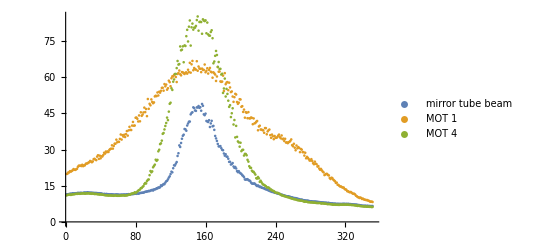

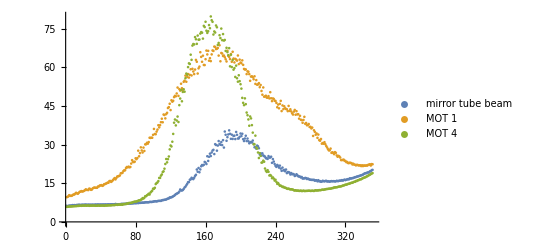

```mathematica
leg={"mirror tube beam","MOT 1", "MOT 4"}
ListPlot[xprojections,PlotLegends->leg]
ListPlot[yprojections,PlotLegends->leg]
```

```mathematica
xfits
```

{}

{a→35.0265,b→34.833,c→10.2797,x0→155.529}

{a→22.337,b→56.5725,c→10.0602,x0→202.702}

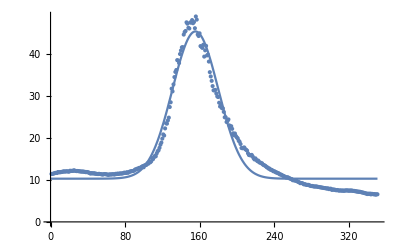

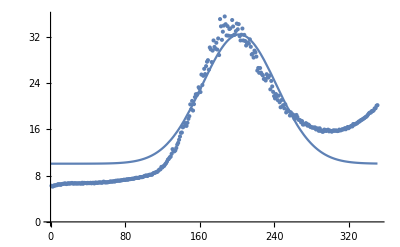

```mathematica
model=a Exp[-(x-x0)^2/b^2]+c;
xproj=Total[images[[1]],{1}];
yproj=Total[images[[1]],{2}];
xfit=FindFit[xproj,model,{{a,40},b,c,{x0,150}},x]
yfit=FindFit[yproj,model,{{a,40},b,c,{x0,150}},x]
(*Show[ListPlot[xproj],Plot[model/.{a->40,b->30,c->10,x0->150},{x,0,xdim},PlotRange->All]]*)
Show[ListPlot[xproj],Plot[model/.xfit,{x,0,xdim},PlotRange->All]]
Show[ListPlot[yproj],Plot[model/.yfit,{x,0,ydim},PlotRange->All]]
```